```mathematica
a=PDF[NormalDistribution[μ,σ],x];
```

```mathematica
μ=0;
σ=10;
```

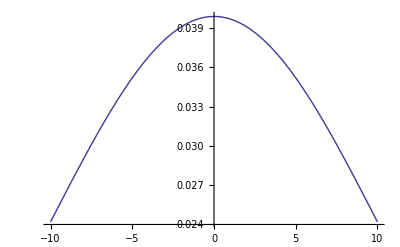

```mathematica
Plot[a,{x,-10,10}]
```

```mathematica
Min[2,3]
```

2

```mathematica
Integrate[PDF[NormalDistribution[μ1,σ1],x],{x,-∞,∞}]
```

ConditionalExpression[1/(√(1/σ1^2) σ1),Re[σ1^2]>0]

```mathematica
Integrate[Min[PDF[NormalDistribution[μ1,σ1],x],PDF[NormalDistribution[μ2,σ2],x]],{x,-∞,∞}]
```

$Aborted

```mathematica
Solve[PDF[NormalDistribution[μ1,σ1],x]==PDF[NormalDistribution[μ2,σ2],x],x]
```

{{x→1/(σ1^2-σ2^2)(μ2 σ1^2-μ1 σ2^2-√(μ1^2 σ1^2 σ2^2-2 μ1 μ2 σ1^2 σ2^2+μ2^2 σ1^2 σ2^2-2 σ1^4 σ2^2 Log[σ2/σ1]+2 σ1^2 σ2^4 Log[σ2/σ1]))},{x→1/(σ1^2-σ2^2)(μ2 σ1^2-μ1 σ2^2+√(μ1^2 σ1^2 σ2^2-2 μ1 μ2 σ1^2 σ2^2+μ2^2 σ1^2 σ2^2-2 σ1^4 σ2^2 Log[σ2/σ1]+2 σ1^2 σ2^4 Log[σ2/σ1]))}}

```mathematica
Simplify[1/(σ1^2-σ2^2)(μ2 σ1^2-μ1 σ2^2+√(μ1^2 σ1^2 σ2^2-2 μ1 μ2 σ1^2 σ2^2+μ2^2 σ1^2 σ2^2-2 σ1^4 σ2^2 Log[σ2/σ1]+2 σ1^2 σ2^4 Log[σ2/σ1]))]
```

(μ2 σ1^2-μ1 σ2^2+√(σ1^2 σ2^2 ((μ1-μ2)^2-2 (σ1^2-σ2^2) Log[σ2/σ1])))/(σ1^2-σ2^2)

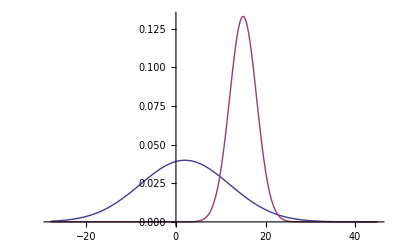

0.245111

```mathematica
μ1=2;
σ1=10;
μ2=15;
σ2=3;
a=PDF[NormalDistribution[μ1,σ1],x];
b=PDF[NormalDistribution[μ2,σ2],x];
Plot[{a,b},{x,Min[μ1,μ2]-3*Max[σ1,σ2],Max[μ1,μ2]+3*Max[σ1,σ2]},PlotRange->Full]
NIntegrate[Min[a,b],{x,Min[μ1,μ2]-3*Max[σ1,σ2],Max[μ1,μ2]+3*Max[σ1,σ2]}]
```

```mathematica
Solve[a==b,x]
```

{{x→3}}

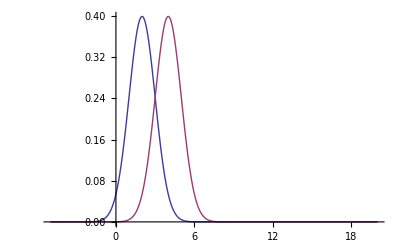

```mathematica
Plot[{a,b},{x,-5,20},PlotRange->Full]
```

```mathematica
NIntegrate[Min[a,b],{x,Min[μ1,μ2]-5*Max[σ1,σ2],Max[μ1,μ2]+5*Max[σ1,σ2]}]
```

0.317311

```mathematica
0.3173099345597714
```

```mathematica
0.31731050786035814
```